In this notebook is simulated a One UnR gene with GA and the three-stage model (burst expression). The notebook has two parts:
1. To evaluate the “sensitivity” to the whole set the parameters. With an arbitrary start point to calculate the estimates (FF, CV2,Mean) (30% of the total number of iterations are removed to estimate these values in the steady-state), and different number of iterations to get a final t of 1500. 
3. To evaluate 4 specific regions

## Parameters for the two sessions

These are the ranges of values for parameters variation. The range of each parameter is divided into smaller ranges (subRanges). In this way the complete range is evaluated in parallel files each one with a subRange of parameters values.

```mathematica
name=0.5; (* This is the last value of the range for the parameter being evluated *)
kgs=Range[0.01,1,0.01];
γgs=Range[0.02,name,0.02]; (* subRanges: 0.02-0.5, 0.52-1.0, 1.02-1.5, 1.52-2 *)
γms=Range[0.001,0.1(*name*),0.001];(* subRanges: 0.001-0.025, 0.026-0.05, 0.051-0.075, 0.076-0.1 *)
γps=Range[0.001,0.1(*name*),0.001];(* subRanges: 0.001-0.025, 0.026-0.05, 0.051-0.075, 0.076-0.1 *)
parametro="γg";(* With the name of the second parameter is named the output file *)
```

These are the default values of parameters

```mathematica
kgA=2;(* Gene activation rate (t^-1)*)
γgA= 0.05;(* Gene desactivation rate (t^-1) *)
kmA=0.696;(* Production rate of mRNA (molecules*t^-1) *)
γmA=0.02082 ;(* mRNA Degradation rate (molecules*t^-1) *)
kpA=1.386;(* Production rate of proteins (molecules*t^-1) *)
γpA=0.02082;(* Degradation rate (molecules*t^-1) *)
(*THESE PARAMETERS ARE A GOOD CHOICE BECAUSE THE NOISE PATTERNS CAN BE SEEN AND NOT SO MANY ITERATIONS ARE REQUIRED TO REACH THE STABLE STATE DUE TO THE DEGRADATION/PRODUCTION RATIO*)
```

## Functions for the two sessions

These are the reactions (changesByRXN) and propensity functions (pF) of the GA for an unRegulated gene

```mathematica
changesByRXN=Function/@<|1->{#1,#2,#3-1,#4+1},2->{#1,#2,#3+1,#4-1},3->{#1+1,#2,#3,#4},4->{#1-1,#2,#3,#4},5->{#1,#2+1,#3,#4},6->{#1,#2-1,#3,#4}|>;(* Each hash represents a specie: mRNA,protein,da0:promoterInactivated,da1:promoterActivated. The numbers are the next reactions: 1-activation, 2-deactivation, 3-5 synthesis, 4-6 degradation *)

pF=Compile[{{kg,_Real},{γg,_Real},{km,_Real},{γm,_Real},{kp,_Real},{γp,_Real},{a,_Integer},{p,_Integer},{da0,_Integer},{da1,_Integer}},{da0*kg,da1*γg,da1*km+0.01(*This allows a basal expression*),a*γm,kp*a,γp*p},RuntimeAttributes->{Listable},Parallelization->True];
```

This is equal for all  sub-circuits

```mathematica
ff[dato_]:=N[Variance[dato]/Mean[dato]]
cv[data_]:=N[StandardDeviation[data]/Mean[data]]
cv2[data_]:=cv[data]^2
```

```mathematica
(* This is the algorithm to estimate the Steady State start from Kelly and Hedengren 2013 *)steadyStateStart[window_,listData_]:=Block[{n,dataByWindow,mPorVentana,μ,sd,probabilidades},
n=Floor[Length[#]/window]&[listData];
dataByWindow=Partition[#,n]&[listData[[All,2]]];mPorVentana=Map[Mean[#[[2;;All]]-#[[1;;-2]]]&,dataByWindow];μ=MapThread[(1/n)(Total[#1]-#2*Total[Range[1,n](*tPorVentana*)])&,{dataByWindow,mPorVentana}];sd=Table[Sqrt[(1/(n-2))*Sum[(dataByWindow[[i,j]]-mPorVentana[[i]]*j-μ[[i]])^2,{j,1,Length[dataByWindow[[i]]]}]],{i,window}];probabilidades=Map[Total[#]/n&,Table[If[Abs[dataByWindow[[i,j]]-μ[[i]]]≤sd[[i]],1,0],{i,window},{j,1,n}]]//N;
((Position[probabilidades,x_/;x>0.1][[1,1]]-1)*n)+1]
```

```mathematica
(* This plots the temporal dynamic of genes mRNA and proteins with log scale *)plotsLogExpression[rep_,ini_,listDataAndTimeTN_,mRNAffcv2MeanA_,proteinffcv2MeanA_,parametros_]:=Module[{datesListAm,datesListAp},
SetOptions[ListLogPlot,Frame-> True,ImageSize->Medium,Joined->True];

{datesListAm,datesListAp}=Table[Transpose[{listDataAndTimeTN[[All,All,1]][[rep]],listDataAndTimeTN[[All,All,2]][[rep,All,i]]}],{i,2}];{ListLogPlot[datesListAm[[ini;;]],PlotStyle->
RGBColor[0.2,0.6,1],FrameLabel->{"time","mRNA A molecules"},PlotLabel->labelA],
ListLogPlot[datesListAp[[ini;;]],PlotStyle->
RGBColor[0.2,0.8,1],FrameLabel->{"time","protein A molecules"},PlotLabel->labelAp]}]
```

## S1: All range parameters values

### Parameters

```mathematica
iteraciones1=400000; (* Number of algorithm iterations *)
replicas1=100; (* Number of times the algorithm is run *)
```

### Simulation

```mathematica
(* Launch the number of kernels in which you will parallelize the simulation *)
LaunchKernels[8]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

This function runs the GA algorithm and processes the output according to the previous functions.

```mathematica
DistributeDefinitions[changesByRXN, pF, ff, cv,cv2, steadyStateStart,
     iteraciones1, kgA, γgA, kmA, γmA, kpA, γpA]; 
(*List by parameters*)
(*    mRNAffcv2ListA = {}; 
    proteinffcv2ListA = {}; *)

Do[
(*List by replicates*)
    listEstimatemRNAA = {};
    listEstimateproteinA = {};
   listDataAndTimeT={};

SetSharedVariable[listEstimatemRNAA,listEstimateproteinA,listDataAndTimeT];

ParallelDo[
       
 listDataAndTime = CreateDataStructure["OrderedHashSet"];
        t = 0;
        abundancia = {1, 1, 1, 0}(*mRNAA,proteinA,da0A,da1A*);
        
Do[τis=Map[If[# > 0,RandomVariate[ExponentialDistribution[#]],∞]&  ,pF[kgA, γgA, kmA, γmA, kpA, γpA, Sequence@@ abundancia]];
            reactionAndτμ = {FirstPosition[#, Min[#]], Min[#]}&[τis];
            abundancia = Through[{reactionAndτμ[[1]] /. changesByRXN}[[1, 1]] @@ abundancia][[1]];
            t = t + reactionAndτμ[[2]];
            listDataAndTime["Union", {{t, abundancia}}];
            If[Length[#]>3&&#[[2]]==5&[IntegerDigits[Round[t]]](* para que Break a los 1500*), Break[]],iteraciones1 ];
      
  listData = Normal[listDataAndTime][[All, 2]];
        ini =Round[(Length[listData]*30)/100.] (*el estado estable se considera depués del 30% de iteraciones *);
(*ini = steadyStateStart[window,listData];*)
        {mRNAffcv2ItA, proteinffcv2ItA} = Table[{ff[i], cv[i],cv2[i], Mean[i],StandardDeviation[i],Variance[i],Table[Moment[i,j],{j,10}],Table[CentralMoment[i,j],{j,10}]}, {i, {listData[[ini ;; All, 1]], listData[[ini ;; All, 2]]}}];
       
   AppendTo[listEstimatemRNAA, mRNAffcv2ItA];
        AppendTo[listEstimateproteinA, proteinffcv2ItA];
       AppendTo[listDataAndTimeT, listDataAndTime];
        
        ,
        replicas1
    ];
     
    ,
 {kgA,{1}},{γgA,{0.2}}]; (*CAMBIAR AQUI EN EL .m*)
```

```mathematica
Export["controlUnRGA_"<>parametro<>ToString[name]<>".csv",{listEstimatemRNAA,listEstimateproteinA}];
```

```mathematica
(************************************************************************* {kgA,{1}},{γgA,{0.2}} ****)
```

```mathematica
listDataAndTimeTN4=Normal/@listDataAndTimeT;
```

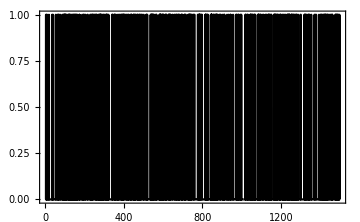
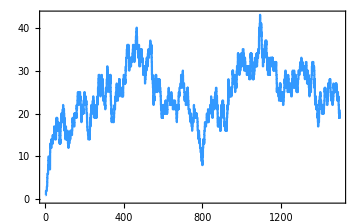
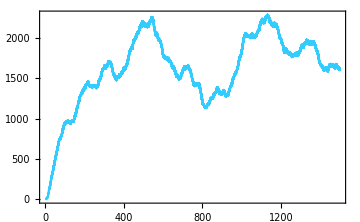

```mathematica
Apply[ListPlot[Transpose[{listDataAndTimeTN4[[1,All,1]],listDataAndTimeTN4[[1,All,2,#]]}],Frame->True,Joined->True,ImageSize->Medium,PlotStyle->
#2,FrameTicksStyle->Directive[Black, 17]]&]/@{{3,Black},{1,RGBColor[0.2,0.6,1]},{2,RGBColor[0.2,0.8,1]}}
```

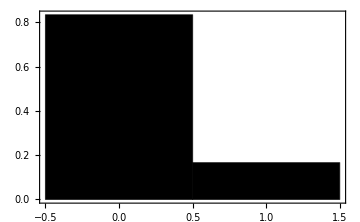
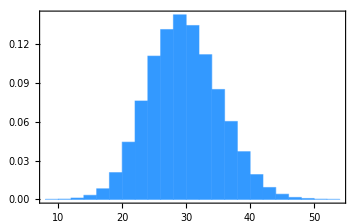
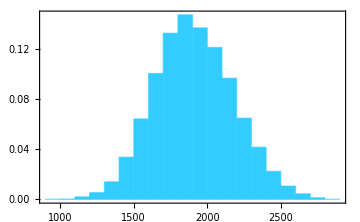

```mathematica
Apply[Histogram[listDataAndTimeTN4[[All,6000;;-1,2,#]]//Flatten,Automatic,"Probability",Frame->True,ImageSize->Medium,FrameTicksStyle->Directive[Black, 17],ChartStyle->
#2]&]/@{{3,Black},{1,RGBColor[0.2,0.6,1]},{2,RGBColor[0.2,0.8,1]}}
```

```mathematica
(************************************************************************* {kgA,{1}},{γgA,{2}} ****)
```

```mathematica
listDataAndTimeTN3=Normal/@listDataAndTimeT;
```

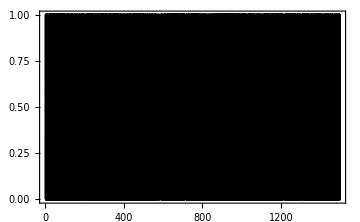
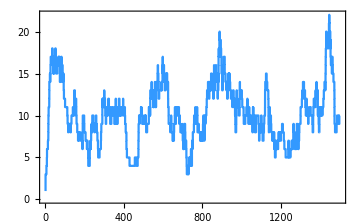
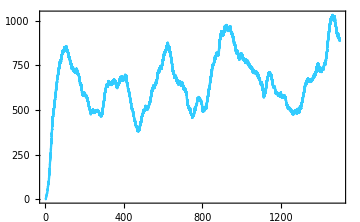

```mathematica
Apply[ListPlot[Transpose[{listDataAndTimeTN3[[1,All,1]],listDataAndTimeTN3[[1,All,2,#]]}],Frame->True,Joined->True,ImageSize->Medium,PlotStyle->
#2,FrameTicksStyle->Directive[Black, 17]]&]/@{{3,Black},{1,RGBColor[0.2,0.6,1]},{2,RGBColor[0.2,0.8,1]}}
```

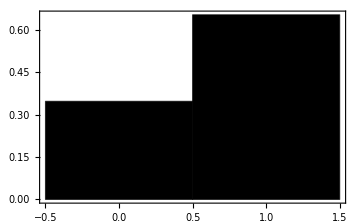
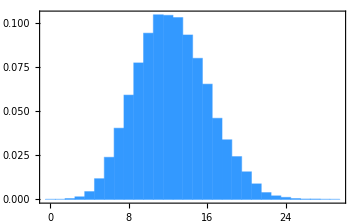
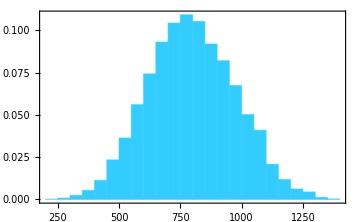

```mathematica
Apply[Histogram[listDataAndTimeTN3[[All,1000;;-1,2,#]]//Flatten,Automatic,"Probability",Frame->True,ImageSize->Medium,FrameTicksStyle->Directive[Black, 17],ChartStyle->
#2]&]/@{{3,Black},{1,RGBColor[0.2,0.6,1]},{2,RGBColor[0.2,0.8,1]}}
```

```mathematica
(************************************************************************* {kgA,{0.05}},{γgA,{0.2}} ****)
```

```mathematica
listDataAndTimeTN2=Normal/@listDataAndTimeT;
```

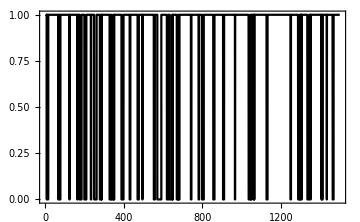
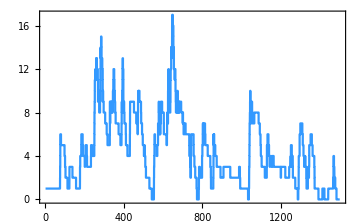
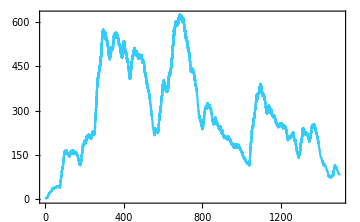

```mathematica
Apply[ListPlot[Transpose[{listDataAndTimeTN2[[1,All,1]],listDataAndTimeTN2[[1,All,2,#]]}],Frame->True,Joined->True,ImageSize->Medium,PlotStyle->
#2,FrameTicksStyle->Directive[Black, 17]]&]/@{{3,Black},{1,RGBColor[0.2,0.6,1]},{2,RGBColor[0.2,0.8,1]}}
```

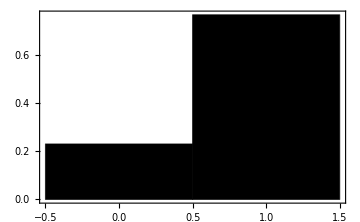
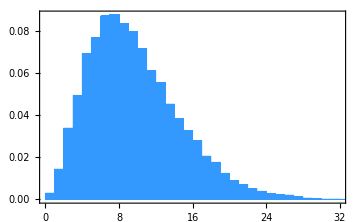
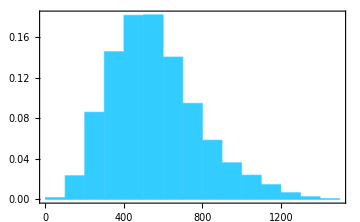

```mathematica
Apply[Histogram[listDataAndTimeTN2[[All,1000;;-1,2,#]]//Flatten,Automatic,"Probability",Frame->True,ImageSize->Medium,FrameTicksStyle->Directive[Black, 17],ChartStyle->
#2]&]/@{{3,Black},{1,RGBColor[0.2,0.6,1]},{2,RGBColor[0.2,0.8,1]}}
```

```mathematica
(*****************************************************************************)
```

```mathematica
listDataAndTimeTN1=Normal/@listDataAndTimeT;
```

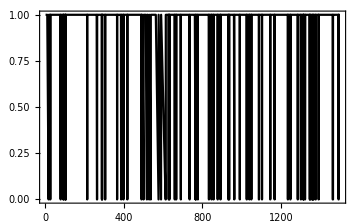
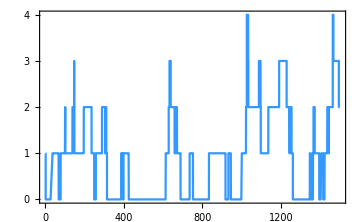
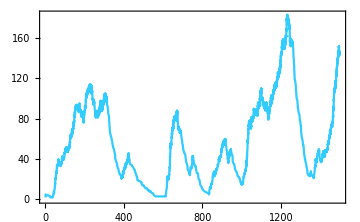

```mathematica
Apply[ListPlot[Transpose[{listDataAndTimeTN[[1,All,1]],listDataAndTimeTN[[1,All,2,#]]}],Frame->True,Joined->True,ImageSize->Medium,PlotStyle->
#2,FrameTicksStyle->Directive[Black, 17]]&]/@{{3,Black},{1,RGBColor[0.2,0.6,1]},{2,RGBColor[0.2,0.8,1]}}
```

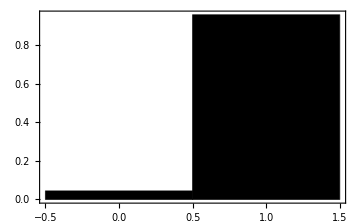
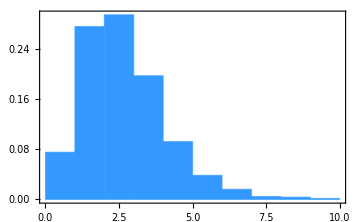
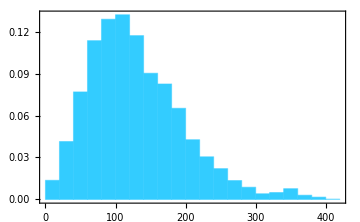

```mathematica
Apply[Histogram[listDataAndTimeTN[[All,1000;;-1,2,#]]//Flatten,Automatic,"Probability",Frame->True,ImageSize->Medium,FrameTicksStyle->Directive[Black, 17],ChartStyle->
#2]&]/@{{3,Black},{1,RGBColor[0.2,0.6,1]},{2,RGBColor[0.2,0.8,1]}}
```

## S2: Evaluation by regions

### Parameters

```mathematica
iteraciones2=400000; (* Number of algorithm iterations *)
replicas2=5; (* Number of times the algorithm is run *)
rep=1; (* Some plots are made with the output of this replicate*)
lagStep=10; (* Lag time for the Autocorrelation plot *)
species=2;(*mRNA genA protein genA*)
```

### Functions

These functions make different plots of the temporal genes expression

```mathematica
(* This plots the temporal dynamic of genes mRNA and proteins *)plotsExpression[rep_,listDataAndTimeTN_,mRNAffcv2MeanA_,proteinffcv2MeanA_,parametros_]:=Module[{datesListAm,datesListAp},
SetOptions[ListLinePlot,Frame-> True,ImageSize->Medium];

{datesListAm,datesListAp}=Table[Transpose[{listDataAndTimeTN[[All,All,1]][[rep]],listDataAndTimeTN[[All,All,2]][[rep,All,i]]}],{i,2}];{ListLinePlot[datesListAm,PlotStyle->
RGBColor[0.2,0.6,1],FrameLabel->{"time","mRNA B molecules"},PlotLabel->labelA],
ListLinePlot[datesListAp,PlotStyle->
RGBColor[0.2,0.8,1],FrameLabel->{"time","protein B molecules"},PlotLabel->labelAp]}]
```

```mathematica
(* This plots the temporal dynamic of genes mRNA and proteins with log scale *)plotsLogExpression[rep_,ini_,listDataAndTimeTN_,mRNAffcv2MeanA_,proteinffcv2MeanA_,parametros_]:=Module[{datesListAm,datesListAp},
SetOptions[ListLogPlot,Frame-> True,ImageSize->Medium,Joined->True];

{datesListAm,datesListAp}=Table[Transpose[{listDataAndTimeTN[[All,All,1]][[rep]],listDataAndTimeTN[[All,All,2]][[rep,All,i]]}],{i,2}];{ListLogPlot[datesListAm[[ini;;]],PlotStyle->
RGBColor[0.2,0.6,1],FrameLabel->{"time","mRNA B molecules"},PlotLabel->labelA],
ListLogPlot[datesListAp[[ini;;]],PlotStyle->
RGBColor[0.2,0.8,1],FrameLabel->{"time","protein B molecules"},PlotLabel->labelAp]}]
```

```mathematica
(* This plots the auto-correlation of the temporal dynamic of genes mRNA and proteins *)autoCorrPlot[lagStep_,listDataAndTimeTN_,positions_]:=Module[{data,lenght,data2,corr,negatives,cortes},
data=Table[MapThread[Extract[#1,#2]&,{listDataAndTimeTN[[All,All,2]][[All,All,i]],positions}],{i,{1,2}}];
lenght=Min[Length/@#]&/@data;
data2=MapThread[TemporalData[#1[[All,1;;#2]],{Range[1,#2]}]&,{data,lenght}](*This is to get the corr in each lag time as the average between replicates *);
DistributeDefinitions[data,data2];
corr=ParallelMap[CorrelationFunction[#,{1,#["PathLengths"][[1]]-1,lagStep}]&,data2];
negatives=FirstPosition[Normal[#],{_,_?Negative}]*lagStep&/@corr;
cortes=Count[Partition[#//Normal,2,1],{{_,_?Positive},{_,_?Negative}}|{{_,_?Negative},{_,_?Positive}}]&/@corr;
ListPlot[#[[1]],Filling->Axis ,Frame->True,ImageSize->Medium,FrameLabel->{"Lag-"<>ToString[lagStep],#[[2]]},PlotStyle->#[[4]],PlotLabel->"First negative: "<>ToString[#[[3]]]<>"\n cortes: "<>ToString[#[[5]]]]&/@{{corr[[1]],"mRNA A",negatives[[1]],RGBColor[0.2,0.6,1],cortes[[1]]},{corr[[2]],"protein A",negatives[[2]],RGBColor[0.2,0.8,1],cortes[[2]]}}]
```

```mathematica
(* This plots the histogram of the steady state gene expression for mRNA and proteins *)distriPlot[ini_,listDataAndTimeTN_]:=Module[{distribucionAm,distribucionAp},
{distribucionAm,distribucionAp}=Table[Flatten[listDataAndTimeTN[[All,All,2]][[All,ini;;All,i]]],{i,2}];Histogram[#[[1]],Automatic(*{Min[#[[1]]]//Round,Max[#[[1]]]//Round,5}*),"Probability",FrameLabel->{#[[2]],"Probability"},PlotLabel->#[[4]]<>" \n FF: "<>ToString[ff[#[[1]]]]<>", CV^2: "<>ToString[expressionNoise[#[[1]]]]<>", Mean: "<>ToString[Mean[#[[1]]]//N],ChartStyle->#[[3]],Frame->True,ImageSize->Medium]&/@{{distribucionAm,"mRNA B molecules",RGBColor[0.2,0.6,1],labelA},{distribucionAp,"protein B molecules",RGBColor[0.2,0.8,1],labelAp}}]
```

```mathematica
(* This plots the velocity of the temporal dynamic of  gene expression *)veloPlot[rep_,listDataAndTimeTN_,positionsVelocity_]:=Module[{listS,listT,velocidades},
listS=Table[Extract[#[[All,i]],positionsVelocity],{i,2}]&[listDataAndTimeTN[[rep,All,2]]];
listT=Extract[#,positionsVelocity]&[listDataAndTimeTN[[rep,All,1]]];
velocidades=Table[(listS[[i,2;;]]-listS[[i,;;-2]])/(listT[[2;;]]-listT[[;;-2]]),{i,2}];
Table[ListLinePlot[Transpose[{listT[[2;;]],velocidades[[i[[1]]]]}],PlotStyle->i[[2]],PlotLabel->"Velocities",FrameLabel->{"time",i[[3]]}],{i,{{1,RGBColor[0.2,0.6,1],"mRNA A molecules"},{2,RGBColor[0.2,0.8,1],"protein A molecules"}}}]]
```

Here there is a detail that changes by sub-circuit : the number and type of Kmm (put it in the arguments of the function simu, in the DistributeDefinitions, and pF function)

This function runs the GA algorithm and processes the output according to the previous functions.

```mathematica
simu[iteraciones_,replicas_,kgA_,γgA_,kmA_,γmA_,kpA_,γpA_,rep_,parametros_,lagStep_,species_]:=

Module[{ini,listEstimatemRNAA,listEstimateproteinA,listEstimatemRNAI,listEstimateproteinI,listDataAndTimeT,listDataAndTime,t,abundancia,τis,reactionAndτμ,listData,mRNAffcv2ItA,proteinffcv2ItA,mRNAffcv2ItI,proteinffcv2ItI,mRNAffcv2MeanA,proteinffcv2MeanA,mRNAffcv2MeanI,proteinffcv2MeanI,listDataAndTimeTN,positions},

DistributeDefinitions[changesByRXN,pF,ff,expressionNoise,steadyStateStart,iteraciones,ini,kgA,γgA,kmA,γmA,kpA,γpA];

listEstimatemRNAA={};
listEstimateproteinA={};
listDataAndTimeT={};

SetSharedVariable[listEstimatemRNAA,listEstimateproteinA,listDataAndTimeT];

ParallelDo[

listDataAndTime=CreateDataStructure["OrderedHashSet"];
t=0;
abundancia={1,1,1,0}(*mRNAA,proteinA,da0A,da1A*);


Do[
          τis=Map[If[#>0,RandomVariate[ExponentialDistribution[#]],∞]&,pF[kgA,γgA,kmA,γmA,kpA,γpA,Sequence@@abundancia]];reactionAndτμ={FirstPosition[#,Min[#]],Min[#]}&[τis];abundancia=Through[{reactionAndτμ[[1]]/.changesByRXN}[[1,1]]@@abundancia][[1]];t=t+reactionAndτμ[[2]];listDataAndTime["Union",{{t,abundancia}}];
If[Length[#]>3&&#[[2]]==5&[IntegerDigits[Round[t]]](* para que Break a los 1500*), Break[]],iteraciones];

listData=Normal[listDataAndTime][[All,2]];
 ini =Round[(Length[listData]*30)/100.];

{mRNAffcv2ItA,proteinffcv2ItA}=Table[{ff[Flatten@i],expressionNoise[Flatten@i],Mean[Flatten@i]//N},{i,{listData[[ini;;All,1]],
listData[[ini;;All,2]]}}];

AppendTo[listEstimatemRNAA,mRNAffcv2ItA];
AppendTo[listEstimateproteinA,proteinffcv2ItA];
AppendTo[listDataAndTimeT,listDataAndTime];,

replicas];

mRNAffcv2MeanA=Mean[listEstimatemRNAA];
proteinffcv2MeanA=Mean[listEstimateproteinA];

Export["controlUnRGA_"<>parametros<>".csv",{listEstimatemRNAA,listEstimateproteinA}];

listDataAndTimeTN=Normal/@listDataAndTimeT;

{labelA,labelAp}=Table["FF: "<>ToString[i[[1]]]<>" CV2: "<>ToString[i[[2]]]<>" Mean: "<>ToString[i[[3]]]<>parametros,{i,{mRNAffcv2MeanA,proteinffcv2MeanA}}];

 ini =Round[(Length[listDataAndTimeTN[[rep]]]*30)/100.];

positions=Table[DeleteCases[FirstPosition[listDataAndTimeTN[[i,All,1]]//Round,#]&/@Range[1,1500,1],Missing["NotFound"]],{i,replicas}];(* These are the positions the ~1500 points to get the velocities and the auto-correlation plot*)

{plotsExpression[rep,listDataAndTimeTN,mRNAffcv2MeanA,proteinffcv2MeanA,parametros],
plotsLogExpression[rep,ini,listDataAndTimeTN,mRNAffcv2MeanA,proteinffcv2MeanA,parametros],
autoCorrPlot[lagStep,listDataAndTimeTN,positions],
distriPlot[ini,listDataAndTimeTN],
veloPlot[rep,listDataAndTimeTN,positions[[rep]]],listDataAndTimeT}]
```

### Simulation

```mathematica
s=Flatten[Table[simu[iteraciones2,replicas2,kgA,γgA,kmA,γmA,kpA,γpA,rep,"\n kgA: " <>ToString[kgA]<>" γgA: "<>ToString[γgA](*parametros*),lagStep,species],{kgA,{0.05,1}},{γgA,{0.2,2}}],{3}];
```

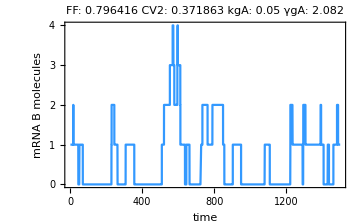
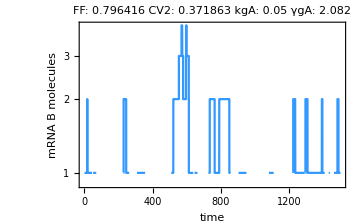
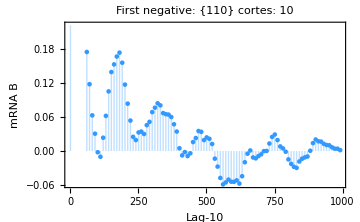
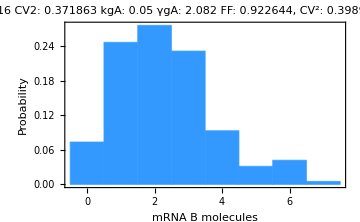
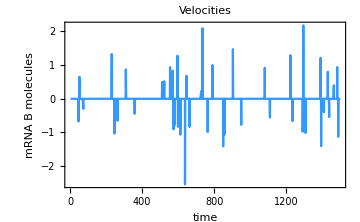
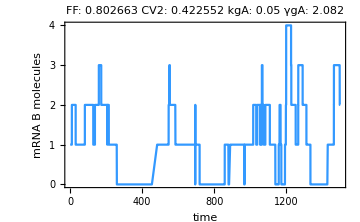
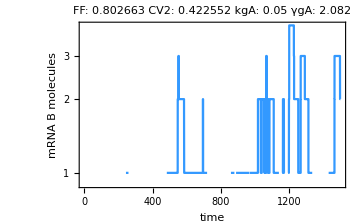
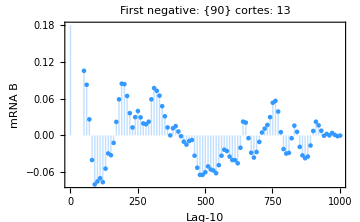
{{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,DataStructure[OrderedHashSet, {Data -> {{1.1877, {1, 2, 1, 0}}, {1.56023, {1, 3, 1, 0}}, {2.51132, {1, 4, 1, 0}}, {2.84574, {1, 5, 1, 0}}, {3.53959, {1, 6, 1, 0}}, {4.82501, {1, 7, 1, 0}}, {5.14616, {1, 6, 1, 0}}, {5.1803, {1, 6, 0, 1}}, {5.34901, {1, <<2>>, 1}}, <<2958>>, {1496.84, {1, 57, 1, 0}}, {1497.96, {1, 56, 1, 0}}, {1498.11, {1, 57, 1, 0}}, {1499.52, {1, 56, 1, 0}}}}]},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,DataStructure[OrderedHashSet, {Data -> {{0.536942, {1, 2, 1, 0}}, {0.575462, {1, 3, 1, 0}}, {0.613548, {1, 4, 1, 0}}, {1.45126, {1, 5, 1, 0}}, {2.9249, {1, 4, 1, 0}}, {3.53947, {1, 5, 1, 0}}, {4.76786, {1, 6, 1, 0}}, {5.77817, {1, 7, 1, 0}}, {6.56178, {<<4>>}}, <<4157>>, {1499.12, {2, 127, 1, 0}}, {1499.21, {2, 128, 1, 0}}, {1499.4, {2, 129, 1, 0}}, {1499.73, {2, 130, 1, 0}}}}]}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,DataStructure[OrderedHashSet, {Data -> {{0.0637806, {1, 1, 0, 1}}, {0.791371, {1, 2, 0, 1}}, {0.860151, {1, 2, 1, 0}}, {0.979113, {1, 3, 1, 0}}, {2.04996, {1, 3, 0, 1}}, {2.81284, {1, 4, 0, 1}}, {3.39269, {1, 5, 0, 1}}, {3.43343, {1, 5, 1, 0}}, {<<2>>}, <<39008>>, {1499.42, {25, 1099, 1, 0}}, {1499.43, {25, 1098, 1, 0}}, {1499.5, {25, 1097, 1, 0}}, {1499.51, {25, 1098, 1, 0}}}}]},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,DataStructure[OrderedHashSet, {Data -> {{0.555708, {1, 2, 1, 0}}, {1.65004, {1, 2, 0, 1}}, {2.59043, {1, 2, 1, 0}}, {4.99397, {1, 2, 0, 1}}, {5.01653, {1, 3, 0, 1}}, {5.16325, {1, 2, 0, 1}}, {5.36304, {1, 3, 0, 1}}, {5.40527, {2, 3, 0, 1}}, {<<2>>}, <<44401>>, {1499.46, {15, 1103, 0, 1}}, {1499.47, {14, 1103, 0, 1}}, {1499.48, {14, 1103, 1, 0}}, {1499.51, {14, 1102, 1, 0}}}}]}}},{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,DataStructure[OrderedHashSet, {Data -> {{0.110551, {1, 2, 1, 0}}, {0.509732, {1, 3, 1, 0}}, {0.739065, {1, 4, 1, 0}}, {0.827727, {1, 5, 1, 0}}, {0.851451, {1, 6, 1, 0}}, {2.90245, {1, 7, 1, 0}}, {3.49903, {1, 6, 1, 0}}, {4.40447, {1, 7, 1, 0}}, {<<6>>2, <<1>>}, <<6558>>, {1499.11, {2, 226, 1, 0}}, {1499.37, {2, 225, 1, 0}}, {1499.41, {2, 224, 1, 0}}, {1499.87, {2, 225, 1, 0}}}}]},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,DataStructure[OrderedHashSet, {Data -> {{0.131896, {1, 2, 1, 0}}, {0.8879, {1, 3, 1, 0}}, {1.95313, {1, 4, 1, 0}}, {2.60979, {1, 5, 1, 0}}, {2.62946, {1, 6, 1, 0}}, {3.08256, {1, 5, 1, 0}}, {3.42625, {1, 6, 1, 0}}, {4.29276, {1, 7, 1, 0}}, {4.41429, {1, <<3>>}}, <<3958>>, {1499.03, {2, 122, 1, 0}}, {1499.14, {2, 121, 1, 0}}, {1499.2, {2, 120, 1, 0}}, {1499.67, {2, 119, 1, 0}}}}]}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,DataStructure[OrderedHashSet, {Data -> {{0.392521, {1, 1, 0, 1}}, {0.725793, {1, 1, 1, 0}}, {1.10115, {1, 2, 1, 0}}, {1.30148, {1, 2, 0, 1}}, {2.59447, {1, 2, 1, 0}}, {3.42647, {1, 3, 1, 0}}, {3.43318, {1, 3, 0, 1}}, {3.63407, {1, 4, 0, 1}}, {3.79365, {<<4>>}}, <<42069>>, {1499.36, {7, 461, 0, 1}}, {1499.47, {7, 462, 0, 1}}, {1499.48, {7, 461, 0, 1}}, {1499.5, {7, 462, 0, 1}}}}]},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,DataStructure[OrderedHashSet, {Data -> {{0.301745, {1, 2, 1, 0}}, {1.06329, {1, 3, 1, 0}}, {1.16923, {1, 4, 1, 0}}, {1.62807, {1, 4, 0, 1}}, {1.81367, {2, 4, 0, 1}}, {2.00326, {2, 4, 1, 0}}, {2.33339, {2, 5, 1, 0}}, {2.34904, {2, 4, 1, 0}}, {<<2>>}, <<46706>>, {1499.47, {17, 1111, 1, 0}}, {1499.48, {17, 1110, 1, 0}}, {1499.49, {17, 1109, 1, 0}}, {1499.52, {17, 1110, 1, 0}}}}]}}},{{{DataStructure[OrderedHashSet, {Data -> {{1.11617, {1, 2, 1, 0}}, {1.1231, {1, 3, 1, 0}}, {1.13868, {1, 4, 1, 0}}, {1.21946, {1, 3, 1, 0}}, {1.22373, {1, 4, 1, 0}}, {2.16399, {1, 5, 1, 0}}, {3.03309, {1, 6, 1, 0}}, {3.47659, {1, 7, 1, 0}}, {4.41898, {1, <<2>>, 0}}, <<6460>>, {1495.61, {1, 47, 1, 0}}, {1496.39, {1, 48, 1, 0}}, {1498.68, {1, 49, 1, 0}}, {1499.6, {1, 49, 0, 1}}}}]},{DataStructure[OrderedHashSet, {Data -> {{0.285691, {1, 2, 1, 0}}, {0.321667, {1, 3, 1, 0}}, {0.6749, {1, 4, 1, 0}}, {0.982599, {1, 5, 1, 0}}, {0.987133, {1, 6, 1, 0}}, {1.23846, {1, 7, 1, 0}}, {2.0876, {1, 6, 1, 0}}, {2.46095, {1, 7, 1, 0}}, {2.55984, {1, <<3>>}}, <<4684>>, {1497.34, {0, 72, 1, 0}}, {1497.84, {0, 71, 1, 0}}, {1498.17, {0, 70, 1, 0}}, {1500.07, {0, 69, 1, 0}}}}]}},{{DataStructure[OrderedHashSet, {Data -> {{1.47102, {1, 2, 1, 0}}, {2.01165, {1, 3, 1, 0}}, {2.26091, {1, 4, 1, 0}}, {2.44395, {1, 3, 1, 0}}, {4.1514, {1, 4, 1, 0}}, {4.93184, {1, 4, 0, 1}}, {5.10404, {2, 4, 0, 1}}, {5.17346, {2, 5, 0, 1}}, {5.18517, <<1>>}, <<47370>>, {1499.45, {13, 881, 1, 0}}, {1499.46, {13, 882, 1, 0}}, {1499.5, {13, 883, 1, 0}}, {1499.55, {13, 884, 1, 0}}}}]},{DataStructure[OrderedHashSet, {Data -> {{0.513121, {1, 2, 1, 0}}, {0.617401, {1, 3, 1, 0}}, {0.691629, {1, 4, 1, 0}}, {1.23343, {1, 5, 1, 0}}, {1.40371, {1, 6, 1, 0}}, {2.18953, {1, 7, 1, 0}}, {2.30842, {1, 8, 1, 0}}, {2.57103, {1, 9, 1, 0}}, {<<2>>}, <<49396>>, {1499.43, {12, 845, 0, 1}}, {1499.46, {12, 846, 0, 1}}, {1499.47, {12, 847, 0, 1}}, {1499.54, {12, 846, 0, 1}}}}]}}},{{{DataStructure[OrderedHashSet, {Data -> {{2.26228, {1, 2, 1, 0}}, {2.45274, {1, 3, 1, 0}}, {3.04563, {1, 4, 1, 0}}, {3.30586, {1, 5, 1, 0}}, {4.08754, {1, 6, 1, 0}}, {4.18463, {1, 7, 1, 0}}, {5.40441, {1, 8, 1, 0}}, {5.57492, {1, 9, 1, 0}}, {6.22244, {1, <<3>>}}, <<6624>>, {1499.08, {2, 110, 1, 0}}, {1499.1, {2, 109, 1, 0}}, {1499.47, {2, 108, 1, 0}}, {1499.74, {2, 109, 1, 0}}}}]},{DataStructure[OrderedHashSet, {Data -> {{1.45854, {1, 2, 1, 0}}, {1.83328, {1, 3, 1, 0}}, {2.47422, {1, 3, 0, 1}}, {2.67737, {1, 3, 1, 0}}, {2.7924, {1, 4, 1, 0}}, {2.9457, {1, 5, 1, 0}}, {3.03323, {1, 6, 1, 0}}, {3.4546, {1, 7, 1, 0}}, {4.71178, {1, 6, 1, 0}}, <<5972>>, {1499.44, {2, 68, 1, 0}}, {1499.45, {2, 69, 1, 0}}, {1499.48, {2, 70, 1, 0}}, {1499.72, {2, 71, 1, 0}}}}]}},{{DataStructure[OrderedHashSet, {Data -> {{0.431086, {1, 1, 0, 1}}, {0.442571, {2, 1, 0, 1}}, {0.465196, {2, 1, 1, 0}}, {0.491919, {2, 2, 1, 0}}, {0.531517, {2, 3, 1, 0}}, {0.666986, {2, 4, 1, 0}}, {1.65642, {2, 4, 0, 1}}, {1.7179, {2, 4, 1, 0}}, {<<2>>}, <<50888>>, {1499.47, {10, 843, 0, 1}}, {1499.47, {10, 843, 1, 0}}, {1499.49, {10, 844, 1, 0}}, {1499.52, {10, 845, 1, 0}}}}]},{DataStructure[OrderedHashSet, {Data -> {{0.105113, {1, 1, 0, 1}}, {0.152366, {1, 1, 1, 0}}, {0.177655, {1, 1, 0, 1}}, {0.656982, {1, 1, 1, 0}}, {0.984887, {1, 2, 1, 0}}, {1.11008, {1, 3, 1, 0}}, {1.41476, {1, 4, 1, 0}}, {2.19836, {1, 4, 0, 1}}, {<<2>>}, <<53189>>, {1499.39, {10, 750, 0, 1}}, {1499.41, {10, 749, 0, 1}}, {1499.5, {10, 750, 0, 1}}, {1499.5, {10, 749, 0, 1}}}}]}}}}

```mathematica
s
```